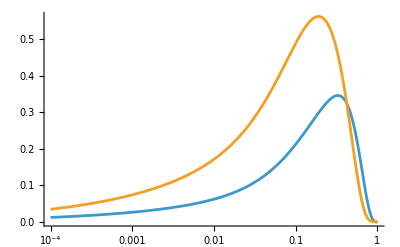

```mathematica
aug[1]=-0.262274329818263;
aug[2]=0.04393992220488276;
aug[3]=-0.004149235660189133;
avu=0.327825081865284;
bvu=5.63913383498245;
bvd=-1.89234339340663;
lan=0.337129653959438;

aaa =2/((Gamma[avu] Gamma[1+bvu])/Gamma[1+avu+bvu]+(7 aug[1] Gamma[avu] Gamma[1+bvu])/Gamma[1+avu+bvu]+(28 aug[2] Gamma[avu] Gamma[1+bvu])/Gamma[1+avu+bvu]+(84 aug[3] Gamma[avu] Gamma[1+bvu])/Gamma[1+avu+bvu]-(14 aug[1] Gamma[1+avu] Gamma[1+bvu])/Gamma[2+avu+bvu]-(126 aug[2] Gamma[1+avu] Gamma[1+bvu])/Gamma[2+avu+bvu]-(630 aug[3] Gamma[1+avu] Gamma[1+bvu])/Gamma[2+avu+bvu]+(126 aug[2] Gamma[2+avu] Gamma[1+bvu])/Gamma[3+avu+bvu]+(1386 aug[3] Gamma[2+avu] Gamma[1+bvu])/Gamma[3+avu+bvu]-(924 aug[3] Gamma[3+avu] Gamma[1+bvu])/Gamma[4+avu+bvu]);
xuvgegn=aaa x^avu(1-x)^bvu(1+∑_(i=1)^3 aug[i]GegenbauerC[i,7/2,1-2x]);


bbb=1/ ((Gamma[avu] Gamma[1+bvd+bvu])/Gamma[1+avu+bvd+bvu]+(7 aug[1] Gamma[avu] Gamma[1+bvd+bvu])/Gamma[1+avu+bvd+bvu]+(28 aug[2] Gamma[avu] Gamma[1+bvd+bvu])/Gamma[1+avu+bvd+bvu]+(84 aug[3] Gamma[avu] Gamma[1+bvd+bvu])/Gamma[1+avu+bvd+bvu]-(14 aug[1] Gamma[1+avu] Gamma[1+bvd+bvu])/Gamma[2+avu+bvd+bvu]-(126 aug[2] Gamma[1+avu] Gamma[1+bvd+bvu])/Gamma[2+avu+bvd+bvu]-(630 aug[3] Gamma[1+avu] Gamma[1+bvd+bvu])/Gamma[2+avu+bvd+bvu]+(126 aug[2] Gamma[2+avu] Gamma[1+bvd+bvu])/Gamma[3+avu+bvd+bvu]+(1386 aug[3] Gamma[2+avu] Gamma[1+bvd+bvu])/Gamma[3+avu+bvd+bvu]-(924 aug[3] Gamma[3+avu] Gamma[1+bvd+bvu])/Gamma[4+avu+bvd+bvu]);


xdvgegen=bbb x^avu(1-x)^bvu(1-x)^bvd(1+∑_(i=1)^3 aug[i]GegenbauerC[i,7/2,1-2x]);

LogLinearPlot[{xdvgegen,xuvgegn},{x,0.0001,1}]
```

```mathematica
Dn=(15 ((0.9275618053002308 Gamma[1+bvu] Gamma[avu+s])/Gamma[1+avu+bvu+s]+(6.492932637101616 aug[1] Gamma[1+bvu] Gamma[avu+s])/Gamma[1+avu+bvu+s]+(25.971730548406462 aug[2] Gamma[1+bvu] Gamma[avu+s])/Gamma[1+avu+bvu+s]+(77.91519164521938 aug[3] Gamma[1+bvu] Gamma[avu+s])/Gamma[1+avu+bvu+s]+(1.5413863209114538 Gamma[1+bvu] Gamma[1+avu+s])/Gamma[2+avu+bvu+s]-(2.196161027823054 aug[1] Gamma[1+bvu] Gamma[1+avu+s])/Gamma[2+avu+bvu+s]-(73.71397048230838 aug[2] Gamma[1+bvu] Gamma[1+avu+s])/Gamma[2+avu+bvu+s]-(454.8874863825833 aug[3] Gamma[1+bvu] Gamma[1+avu+s])/Gamma[2+avu+bvu+s]-(5.109405666082289 Gamma[1+bvu] Gamma[2+avu+s])/Gamma[3+avu+bvu+s]-(57.34524815533638 aug[1] Gamma[1+bvu] Gamma[2+avu+s])/Gamma[3+avu+bvu+s]-(220.4052476173182 aug[2] Gamma[1+bvu] Gamma[2+avu+s])/Gamma[3+avu+bvu+s]-(114.66279597900825 aug[3] Gamma[1+bvu] Gamma[2+avu+s])/Gamma[3+avu+bvu+s]+(4.064017965930289 Gamma[1+bvu] Gamma[3+avu+s])/Gamma[4+avu+bvu+s]+(99.97980508666407 aug[1] Gamma[1+bvu] Gamma[3+avu+s])/Gamma[4+avu+bvu+s]+(951.7922934072598 aug[2] Gamma[1+bvu] Gamma[3+avu+s])/Gamma[4+avu+bvu+s]+(4839.597411455848 aug[3] Gamma[1+bvu] Gamma[3+avu+s])/Gamma[4+avu+bvu+s]-(56.89625152302404 aug[1] Gamma[1+bvu] Gamma[4+avu+s])/Gamma[5+avu+bvu+s]-(1155.851377633585 aug[2] Gamma[1+bvu] Gamma[4+avu+s])/Gamma[5+avu+bvu+s]-(11066.208532248318 aug[3] Gamma[1+bvu] Gamma[4+avu+s])/Gamma[5+avu+bvu+s]+(512.0662637072164 aug[2] Gamma[1+bvu] Gamma[5+avu+s])/Gamma[6+avu+bvu+s]+(10353.819736239415 aug[3] Gamma[1+bvu] Gamma[5+avu+s])/Gamma[6+avu+bvu+s]-(3755.1526005195874 aug[3] Gamma[1+bvu] Gamma[6+avu+s])/Gamma[7+avu+bvu+s]))/(14 ((Gamma[avu] Gamma[1+bvu])/Gamma[1+avu+bvu]+(7 aug[1] Gamma[avu] Gamma[1+bvu])/Gamma[1+avu+bvu]+(28 aug[2] Gamma[avu] Gamma[1+bvu])/Gamma[1+avu+bvu]+(84 aug[3] Gamma[avu] Gamma[1+bvu])/Gamma[1+avu+bvu]-(14 aug[1] Gamma[1+avu] Gamma[1+bvu])/Gamma[2+avu+bvu]-(126 aug[2] Gamma[1+avu] Gamma[1+bvu])/Gamma[2+avu+bvu]-(630 aug[3] Gamma[1+avu] Gamma[1+bvu])/Gamma[2+avu+bvu]+(126 aug[2] Gamma[2+avu] Gamma[1+bvu])/Gamma[3+avu+bvu]+(1386 aug[3] Gamma[2+avu] Gamma[1+bvu])/Gamma[3+avu+bvu]-(924 aug[3] Gamma[3+avu] Gamma[1+bvu])/Gamma[4+avu+bvu]))+(13 ((0.9275618053002308 Gamma[1+bvd+bvu] Gamma[avu+s])/Gamma[1+avu+bvd+bvu+s]+(6.492932637101616 aug[1] Gamma[1+bvd+bvu] Gamma[avu+s])/Gamma[1+avu+bvd+bvu+s]+(25.971730548406462 aug[2] Gamma[1+bvd+bvu] Gamma[avu+s])/Gamma[1+avu+bvd+bvu+s]+(77.91519164521938 aug[3] Gamma[1+bvd+bvu] Gamma[avu+s])/Gamma[1+avu+bvd+bvu+s]+(1.5413863209114538 Gamma[1+bvd+bvu] Gamma[1+avu+s])/Gamma[2+avu+bvd+bvu+s]-(2.196161027823054 aug[1] Gamma[1+bvd+bvu] Gamma[1+avu+s])/Gamma[2+avu+bvd+bvu+s]-(73.71397048230838 aug[2] Gamma[1+bvd+bvu] Gamma[1+avu+s])/Gamma[2+avu+bvd+bvu+s]-(454.8874863825833 aug[3] Gamma[1+bvd+bvu] Gamma[1+avu+s])/Gamma[2+avu+bvd+bvu+s]-(5.109405666082289 Gamma[1+bvd+bvu] Gamma[2+avu+s])/Gamma[3+avu+bvd+bvu+s]-(57.34524815533638 aug[1] Gamma[1+bvd+bvu] Gamma[2+avu+s])/Gamma[3+avu+bvd+bvu+s]-(220.4052476173182 aug[2] Gamma[1+bvd+bvu] Gamma[2+avu+s])/Gamma[3+avu+bvd+bvu+s]-(114.66279597900825 aug[3] Gamma[1+bvd+bvu] Gamma[2+avu+s])/Gamma[3+avu+bvd+bvu+s]+(4.064017965930289 Gamma[1+bvd+bvu] Gamma[3+avu+s])/Gamma[4+avu+bvd+bvu+s]+(99.97980508666407 aug[1] Gamma[1+bvd+bvu] Gamma[3+avu+s])/Gamma[4+avu+bvd+bvu+s]+(951.7922934072598 aug[2] Gamma[1+bvd+bvu] Gamma[3+avu+s])/Gamma[4+avu+bvd+bvu+s]+(4839.597411455848 aug[3] Gamma[1+bvd+bvu] Gamma[3+avu+s])/Gamma[4+avu+bvd+bvu+s]-(56.89625152302404 aug[1] Gamma[1+bvd+bvu] Gamma[4+avu+s])/Gamma[5+avu+bvd+bvu+s]-(1155.851377633585 aug[2] Gamma[1+bvd+bvu] Gamma[4+avu+s])/Gamma[5+avu+bvd+bvu+s]-(11066.208532248318 aug[3] Gamma[1+bvd+bvu] Gamma[4+avu+s])/Gamma[5+avu+bvd+bvu+s]+(512.0662637072164 aug[2] Gamma[1+bvd+bvu] Gamma[5+avu+s])/Gamma[6+avu+bvd+bvu+s]+(10353.819736239415 aug[3] Gamma[1+bvd+bvu] Gamma[5+avu+s])/Gamma[6+avu+bvd+bvu+s]-(3755.1526005195874 aug[3] Gamma[1+bvd+bvu] Gamma[6+avu+s])/Gamma[7+avu+bvd+bvu+s]))/(28 ((Gamma[avu] Gamma[1+bvd+bvu])/Gamma[1+avu+bvd+bvu]+(7 aug[1] Gamma[avu] Gamma[1+bvd+bvu])/Gamma[1+avu+bvd+bvu]+(28 aug[2] Gamma[avu] Gamma[1+bvd+bvu])/Gamma[1+avu+bvd+bvu]+(84 aug[3] Gamma[avu] Gamma[1+bvd+bvu])/Gamma[1+avu+bvd+bvu]-(14 aug[1] Gamma[1+avu] Gamma[1+bvd+bvu])/Gamma[2+avu+bvd+bvu]-(126 aug[2] Gamma[1+avu] Gamma[1+bvd+bvu])/Gamma[2+avu+bvd+bvu]-(630 aug[3] Gamma[1+avu] Gamma[1+bvd+bvu])/Gamma[2+avu+bvd+bvu]+(126 aug[2] Gamma[2+avu] Gamma[1+bvd+bvu])/Gamma[3+avu+bvd+bvu]+(1386 aug[3] Gamma[2+avu] Gamma[1+bvd+bvu])/Gamma[3+avu+bvd+bvu]-(924 aug[3] Gamma[3+avu] Gamma[1+bvd+bvu])/Gamma[4+avu+bvd+bvu]));


Un=(13 (-(0.07232232765081216 Gamma[0.6+bvu] Gamma[avu+s])/Gamma[0.6000000000000001+avu+bvu+s]-(0.5062562935556851 aug[1] Gamma[0.6+bvu] Gamma[avu+s])/Gamma[0.6000000000000001+avu+bvu+s]-(2.0250251742227405 aug[2] Gamma[0.6+bvu] Gamma[avu+s])/Gamma[0.6000000000000001+avu+bvu+s]-(6.075075522668222 aug[3] Gamma[0.6+bvu] Gamma[avu+s])/Gamma[0.6000000000000001+avu+bvu+s]+(Gamma[1+bvu] Gamma[avu+s])/Gamma[1+avu+bvu+s]+(7 aug[1] Gamma[1+bvu] Gamma[avu+s])/Gamma[1+avu+bvu+s]+(28 aug[2] Gamma[1+bvu] Gamma[avu+s])/Gamma[1+avu+bvu+s]+(84 aug[3] Gamma[1+bvu] Gamma[avu+s])/Gamma[1+avu+bvu+s]+(1.5413863209114538 Gamma[0.6+bvu] Gamma[1+avu+s])/Gamma[1.6+avu+bvu+s]+(11.802216833491546 aug[1] Gamma[0.6+bvu] Gamma[1+avu+s])/Gamma[1.6+avu+bvu+s]+(52.27143026952304 aug[2] Gamma[0.6+bvu] Gamma[1+avu+s])/Gamma[1.6+avu+bvu+s]+(175.03951737657377 aug[3] Gamma[0.6+bvu] Gamma[1+avu+s])/Gamma[1.6+avu+bvu+s]-(14 aug[1] Gamma[1+bvu] Gamma[1+avu+s])/Gamma[2+avu+bvu+s]-(126 aug[2] Gamma[1+bvu] Gamma[1+avu+s])/Gamma[2+avu+bvu+s]-(630 aug[3] Gamma[1+bvu] Gamma[1+avu+s])/Gamma[2+avu+bvu+s]-(5.109405666082289 Gamma[0.6+bvu] Gamma[2+avu+s])/Gamma[2.6+avu+bvu+s]-(57.34524815533638 aug[1] Gamma[0.6+bvu] Gamma[2+avu+s])/Gamma[2.6+avu+bvu+s]-(346.39064836914963 aug[2] Gamma[0.6+bvu] Gamma[2+avu+s])/Gamma[2.6+avu+bvu+s]-(1500.5022042491537 aug[3] Gamma[0.6+bvu] Gamma[2+avu+s])/Gamma[2.6+avu+bvu+s]+(126 aug[2] Gamma[1+bvu] Gamma[2+avu+s])/Gamma[3+avu+bvu+s]+(1386 aug[3] Gamma[1+bvu] Gamma[2+avu+s])/Gamma[3+avu+bvu+s]+(4.064017965930289 Gamma[0.6+bvu] Gamma[3+avu+s])/Gamma[3.6+avu+bvu+s]+(99.97980508666407 aug[1] Gamma[0.6+bvu] Gamma[3+avu+s])/Gamma[3.6+avu+bvu+s]+(951.7922934072598 aug[2] Gamma[0.6+bvu] Gamma[3+avu+s])/Gamma[3.6+avu+bvu+s]+(5763.490350302612 aug[3] Gamma[0.6+bvu] Gamma[3+avu+s])/Gamma[3.6+avu+bvu+s]-(924 aug[3] Gamma[1+bvu] Gamma[3+avu+s])/Gamma[4+avu+bvu+s]-(56.89625152302404 aug[1] Gamma[0.6+bvu] Gamma[4+avu+s])/Gamma[4.6+avu+bvu+s]-(1155.851377633585 aug[2] Gamma[0.6+bvu] Gamma[4+avu+s])/Gamma[4.6+avu+bvu+s]-(11066.208532248318 aug[3] Gamma[0.6+bvu] Gamma[4+avu+s])/Gamma[4.6+avu+bvu+s]+(512.0662637072164 aug[2] Gamma[0.6+bvu] Gamma[5+avu+s])/Gamma[5.6+avu+bvu+s]+(10353.819736239415 aug[3] Gamma[0.6+bvu] Gamma[5+avu+s])/Gamma[5.6+avu+bvu+s]-(3755.1526005195874 aug[3] Gamma[0.6+bvu] Gamma[6+avu+s])/Gamma[6.6+avu+bvu+s]))/(14 ((Gamma[avu] Gamma[1+bvu])/Gamma[1+avu+bvu]+(7 aug[1] Gamma[avu] Gamma[1+bvu])/Gamma[1+avu+bvu]+(28 aug[2] Gamma[avu] Gamma[1+bvu])/Gamma[1+avu+bvu]+(84 aug[3] Gamma[avu] Gamma[1+bvu])/Gamma[1+avu+bvu]-(14 aug[1] Gamma[1+avu] Gamma[1+bvu])/Gamma[2+avu+bvu]-(126 aug[2] Gamma[1+avu] Gamma[1+bvu])/Gamma[2+avu+bvu]-(630 aug[3] Gamma[1+avu] Gamma[1+bvu])/Gamma[2+avu+bvu]+(126 aug[2] Gamma[2+avu] Gamma[1+bvu])/Gamma[3+avu+bvu]+(1386 aug[3] Gamma[2+avu] Gamma[1+bvu])/Gamma[3+avu+bvu]-(924 aug[3] Gamma[3+avu] Gamma[1+bvu])/Gamma[4+avu+bvu]))+(15 (-(0.07232232765081216 Gamma[0.6+bvd+bvu] Gamma[avu+s])/Gamma[0.6000000000000001+avu+bvd+bvu+s]-(0.5062562935556851 aug[1] Gamma[0.6+bvd+bvu] Gamma[avu+s])/Gamma[0.6000000000000001+avu+bvd+bvu+s]-(2.0250251742227405 aug[2] Gamma[0.6+bvd+bvu] Gamma[avu+s])/Gamma[0.6000000000000001+avu+bvd+bvu+s]-(6.075075522668222 aug[3] Gamma[0.6+bvd+bvu] Gamma[avu+s])/Gamma[0.6000000000000001+avu+bvd+bvu+s]+(Gamma[1+bvd+bvu] Gamma[avu+s])/Gamma[1+avu+bvd+bvu+s]+(7 aug[1] Gamma[1+bvd+bvu] Gamma[avu+s])/Gamma[1+avu+bvd+bvu+s]+(28 aug[2] Gamma[1+bvd+bvu] Gamma[avu+s])/Gamma[1+avu+bvd+bvu+s]+(84 aug[3] Gamma[1+bvd+bvu] Gamma[avu+s])/Gamma[1+avu+bvd+bvu+s]+(1.5413863209114538 Gamma[0.6+bvd+bvu] Gamma[1+avu+s])/Gamma[1.6+avu+bvd+bvu+s]+(11.802216833491546 aug[1] Gamma[0.6+bvd+bvu] Gamma[1+avu+s])/Gamma[1.6+avu+bvd+bvu+s]+(52.27143026952304 aug[2] Gamma[0.6+bvd+bvu] Gamma[1+avu+s])/Gamma[1.6+avu+bvd+bvu+s]+(175.03951737657377 aug[3] Gamma[0.6+bvd+bvu] Gamma[1+avu+s])/Gamma[1.6+avu+bvd+bvu+s]-(14 aug[1] Gamma[1+bvd+bvu] Gamma[1+avu+s])/Gamma[2+avu+bvd+bvu+s]-(126 aug[2] Gamma[1+bvd+bvu] Gamma[1+avu+s])/Gamma[2+avu+bvd+bvu+s]-(630 aug[3] Gamma[1+bvd+bvu] Gamma[1+avu+s])/Gamma[2+avu+bvd+bvu+s]-(5.109405666082289 Gamma[0.6+bvd+bvu] Gamma[2+avu+s])/Gamma[2.6+avu+bvd+bvu+s]-(57.34524815533638 aug[1] Gamma[0.6+bvd+bvu] Gamma[2+avu+s])/Gamma[2.6+avu+bvd+bvu+s]-(346.39064836914963 aug[2] Gamma[0.6+bvd+bvu] Gamma[2+avu+s])/Gamma[2.6+avu+bvd+bvu+s]-(1500.5022042491537 aug[3] Gamma[0.6+bvd+bvu] Gamma[2+avu+s])/Gamma[2.6+avu+bvd+bvu+s]+(126 aug[2] Gamma[1+bvd+bvu] Gamma[2+avu+s])/Gamma[3+avu+bvd+bvu+s]+(1386 aug[3] Gamma[1+bvd+bvu] Gamma[2+avu+s])/Gamma[3+avu+bvd+bvu+s]+(4.064017965930289 Gamma[0.6+bvd+bvu] Gamma[3+avu+s])/Gamma[3.6+avu+bvd+bvu+s]+(99.97980508666407 aug[1] Gamma[0.6+bvd+bvu] Gamma[3+avu+s])/Gamma[3.6+avu+bvd+bvu+s]+(951.7922934072598 aug[2] Gamma[0.6+bvd+bvu] Gamma[3+avu+s])/Gamma[3.6+avu+bvd+bvu+s]+(5763.490350302612 aug[3] Gamma[0.6+bvd+bvu] Gamma[3+avu+s])/Gamma[3.6+avu+bvd+bvu+s]-(924 aug[3] Gamma[1+bvd+bvu] Gamma[3+avu+s])/Gamma[4+avu+bvd+bvu+s]-(56.89625152302404 aug[1] Gamma[0.6+bvd+bvu] Gamma[4+avu+s])/Gamma[4.6+avu+bvd+bvu+s]-(1155.851377633585 aug[2] Gamma[0.6+bvd+bvu] Gamma[4+avu+s])/Gamma[4.6+avu+bvd+bvu+s]-(11066.208532248318 aug[3] Gamma[0.6+bvd+bvu] Gamma[4+avu+s])/Gamma[4.6+avu+bvd+bvu+s]+(512.0662637072164 aug[2] Gamma[0.6+bvd+bvu] Gamma[5+avu+s])/Gamma[5.6+avu+bvd+bvu+s]+(10353.819736239415 aug[3] Gamma[0.6+bvd+bvu] Gamma[5+avu+s])/Gamma[5.6+avu+bvd+bvu+s]-(3755.1526005195874 aug[3] Gamma[0.6+bvd+bvu] Gamma[6+avu+s])/Gamma[6.6+avu+bvd+bvu+s]))/(28 ((Gamma[avu] Gamma[1+bvd+bvu])/Gamma[1+avu+bvd+bvu]+(7 aug[1] Gamma[avu] Gamma[1+bvd+bvu])/Gamma[1+avu+bvd+bvu]+(28 aug[2] Gamma[avu] Gamma[1+bvd+bvu])/Gamma[1+avu+bvd+bvu]+(84 aug[3] Gamma[avu] Gamma[1+bvd+bvu])/Gamma[1+avu+bvd+bvu]-(14 aug[1] Gamma[1+avu] Gamma[1+bvd+bvu])/Gamma[2+avu+bvd+bvu]-(126 aug[2] Gamma[1+avu] Gamma[1+bvd+bvu])/Gamma[2+avu+bvd+bvu]-(630 aug[3] Gamma[1+avu] Gamma[1+bvd+bvu])/Gamma[2+avu+bvd+bvu]+(126 aug[2] Gamma[2+avu] Gamma[1+bvd+bvu])/Gamma[3+avu+bvd+bvu]+(1386 aug[3] Gamma[2+avu] Gamma[1+bvd+bvu])/Gamma[3+avu+bvd+bvu]-(924 aug[3] Gamma[3+avu] Gamma[1+bvd+bvu])/Gamma[4+avu+bvd+bvu]));
```

```mathematica
Λ=lan^2;
Q0=1;

β0=11-2/3 f;
β1=102-38/3 f;
β2=2857/2-5033/18 f+325/54 f^2;
"Q=Input["Q"]"; 
αQ=4Pi(1/(β0*(y-Log[Λ]))-β1/(β0)^3 Log[y-Log[Λ]]/(y-Log[Λ])^2+1/((β0)^3(y-Log[Λ])^3)((β1)^2/(β0)^2((Log[y-Log[Λ]])^2-(Log[y-Log[Λ]])-1)+(β2)/(β0)));
αQ0=4Pi(1/(β0*(y0-Log[Λ]))-β1/(β0)^3 Log[y0-Log[Λ]]/(y0-Log[Λ])^2+1/((β0)^3(y0-Log[Λ])^3)((β1)^2/(β0)^2((Log[y0-Log[Λ]])^2-(Log[y0-Log[Λ]])-1)+(β2)/(β0)));

AlfasQ=αQ;
AlfasQ0=αQ0;
(*αQ=4Pi(1/(β0*(y-Log[Λ])));
αQ0=4Pi(1/(β0*(y0-Log[Λ])));*)
taQ=Integrate[1/(4Pi)AlfasQ,y]/.y->Log[Q];
taQ0=Integrate[1/(4Pi)AlfasQ0,y0]/.y0->Log[Q0];
ta=taQ-taQ0;
cf=4/3;
ca=3;
 tf=f;
tr=1/2;
(*lan=0.2*)
ta2n=(-(192 (789 β1^4-1400 β0 β1^2 β2+625 β0^2 β2^2))/β0^4+(9375 (-9 β1^3+8 β0 β1 β2) (Log[Q]-Log[Λ]))/β0^2+400000 (β1^2-β0 β2) (Log[Q]-Log[Λ])^2+300000 β0^2 β1 (Log[Q]-Log[Λ])^3-600000 β0^4 (Log[Q]-Log[Λ])^4+1/β0^4 60 β1 (-2624 β1^3+2400 β0 β1 β2-5625 β0^2 β1^2 (Log[Q]-Log[Λ])+5000 β0^3 β2 (Log[Q]-Log[Λ])+10000 β0^6 (Log[Q]-Log[Λ])^3) Log[Log[Q]-Log[Λ]]-1/β0^4 600 β1^2 (-344 β1^2+400 β0 β2+125 β0^2 β1 (Log[Q]-Log[Λ])+1000 β0^4 (Log[Q]-Log[Λ])^2) Log[Log[Q]-Log[Λ]]^2+(12000 β1^3 (12 β1+25 β0^2 (Log[Q]-Log[Λ])) Log[Log[Q]-Log[Λ]]^3)/β0^4-(120000 β1^4 Log[Log[Q]-Log[Λ]]^4)/β0^4)/(600000 β0^6 (Log[Q]-Log[Λ])^5)-(-(192 (789 β1^4-1400 β0 β1^2 β2+625 β0^2 β2^2))/β0^4+(9375 (-9 β1^3+8 β0 β1 β2) (Log[Q0]-Log[Λ]))/β0^2+400000 (β1^2-β0 β2) (Log[Q0]-Log[Λ])^2+300000 β0^2 β1 (Log[Q0]-Log[Λ])^3-600000 β0^4 (Log[Q0]-Log[Λ])^4+1/β0^4 60 β1 (-2624 β1^3+2400 β0 β1 β2-5625 β0^2 β1^2 (Log[Q0]-Log[Λ])+5000 β0^3 β2 (Log[Q0]-Log[Λ])+10000 β0^6 (Log[Q0]-Log[Λ])^3) Log[Log[Q0]-Log[Λ]]-1/β0^4 600 β1^2 (-344 β1^2+400 β0 β2+125 β0^2 β1 (Log[Q0]-Log[Λ])+1000 β0^4 (Log[Q0]-Log[Λ])^2) Log[Log[Q0]-Log[Λ]]^2+(12000 β1^3 (12 β1+25 β0^2 (Log[Q0]-Log[Λ])) Log[Log[Q0]-Log[Λ]]^3)/β0^4-(120000 β1^4 Log[Log[Q0]-Log[Λ]]^4)/β0^4)/(600000 β0^6 (Log[Q0]-Log[Λ])^5);

ta3n=1/β0^9((21703 β1^6-59040 β0 β1^4 β2+53760 β0^2 β1^2 β2^2-16384 β0^3 β2^3)/(131072 β0^6 (Log[Q]-Log[Λ])^8)+(3 (3263 β1^5-5586 β0 β1^3 β2+2401 β0^2 β1 β2^2))/(117649 β0^4 (Log[Q]-Log[Λ])^7)+(-127 β1^4+234 β0 β1^2 β2-108 β0^2 β2^2)/(216 β0^2 (Log[Q]-Log[Λ])^6)+(6 (-28 β1^3+25 β0 β1 β2))/(625 (Log[Q]-Log[Λ])^5)+(3 β0^2 (β1^2-β0 β2))/(4 (Log[Q]-Log[Λ])^4)+(β0^4 β1)/(3 (Log[Q]-Log[Λ])^3)-β0^6/(2 (Log[Q]-Log[Λ])^2)+(β1 (100570987125 β1^5-186961068000 β0 β1^3 β2+87127488000 β0^2 β1 β2^2+180430848000 β0^2 β1^4 (Log[Q]-Log[Λ])-308883456000 β0^3 β1^2 β2 (Log[Q]-Log[Λ])+132765696000 β0^4 β2^2 (Log[Q]-Log[Λ])-163498496000 β0^4 β1^3 (Log[Q]-Log[Λ])^2+154893312000 β0^5 β1 β2 (Log[Q]-Log[Λ])^2-416353222656 β0^6 β1^2 (Log[Q]-Log[Λ])^3+371743948800 β0^7 β2 (Log[Q]-Log[Λ])^3+309786624000 β0^10 (Log[Q]-Log[Λ])^5) Log[Log[Q]-Log[Λ]])/(309786624000 β0^6 (Log[Q]-Log[Λ])^8)-(β1^2 (148561875 β1^4-432180000 β0 β1^2 β2+276595200 β0^2 β2^2-397209600 β0^2 β1^3 (Log[Q]-Log[Λ])+361267200 β0^3 β1 β2 (Log[Q]-Log[Λ])-1044915200 β0^4 β1^2 (Log[Q]-Log[Λ])^2+1106380800 β0^5 β2 (Log[Q]-Log[Λ])^2+265531392 β0^6 β1 (Log[Q]-Log[Λ])^3+1106380800 β0^8 (Log[Q]-Log[Λ])^4) Log[Log[Q]-Log[Λ]]^2)/(737587200 β0^6 (Log[Q]-Log[Λ])^8)+(β1^3 (-1414875 β1^3+1481760 β0 β1 β2-1958400 β0^2 β1^2 (Log[Q]-Log[Λ])+2257920 β0^3 β2 (Log[Q]-Log[Λ])+2195200 β0^4 β1 (Log[Q]-Log[Λ])^2+3687936 β0^6 (Log[Q]-Log[Λ])^3) Log[Log[Q]-Log[Λ]]^3)/(2634240 β0^6 (Log[Q]-Log[Λ])^8)-(β1^4 (-2205 β1^2+4704 β0 β2+6912 β0^2 β1 (Log[Q]-Log[Λ])+12544 β0^4 (Log[Q]-Log[Λ])^2) Log[Log[Q]-Log[Λ]]^4)/(12544 β0^6 (Log[Q]-Log[Λ])^8)+(3 β1^5 (21 β1+32 β0^2 (Log[Q]-Log[Λ])) Log[Log[Q]-Log[Λ]]^5)/(224 β0^6 (Log[Q]-Log[Λ])^8)-(β1^6 Log[Log[Q]-Log[Λ]]^6)/(8 β0^6 (Log[Q]-Log[Λ])^8))-1/β0^9((21703 β1^6-59040 β0 β1^4 β2+53760 β0^2 β1^2 β2^2-16384 β0^3 β2^3)/(131072 β0^6 (Log[Q0]-Log[Λ])^8)+(3 (3263 β1^5-5586 β0 β1^3 β2+2401 β0^2 β1 β2^2))/(117649 β0^4 (Log[Q0]-Log[Λ])^7)+(-127 β1^4+234 β0 β1^2 β2-108 β0^2 β2^2)/(216 β0^2 (Log[Q0]-Log[Λ])^6)+(6 (-28 β1^3+25 β0 β1 β2))/(625 (Log[Q0]-Log[Λ])^5)+(3 β0^2 (β1^2-β0 β2))/(4 (Log[Q0]-Log[Λ])^4)+(β0^4 β1)/(3 (Log[Q0]-Log[Λ])^3)-β0^6/(2 (Log[Q0]-Log[Λ])^2)+(β1 (100570987125 β1^5-186961068000 β0 β1^3 β2+87127488000 β0^2 β1 β2^2+180430848000 β0^2 β1^4 (Log[Q0]-Log[Λ])-308883456000 β0^3 β1^2 β2 (Log[Q0]-Log[Λ])+132765696000 β0^4 β2^2 (Log[Q0]-Log[Λ])-163498496000 β0^4 β1^3 (Log[Q0]-Log[Λ])^2+154893312000 β0^5 β1 β2 (Log[Q0]-Log[Λ])^2-416353222656 β0^6 β1^2 (Log[Q0]-Log[Λ])^3+371743948800 β0^7 β2 (Log[Q0]-Log[Λ])^3+309786624000 β0^10 (Log[Q0]-Log[Λ])^5) Log[Log[Q0]-Log[Λ]])/(309786624000 β0^6 (Log[Q0]-Log[Λ])^8)-(β1^2 (148561875 β1^4-432180000 β0 β1^2 β2+276595200 β0^2 β2^2-397209600 β0^2 β1^3 (Log[Q0]-Log[Λ])+361267200 β0^3 β1 β2 (Log[Q0]-Log[Λ])-1044915200 β0^4 β1^2 (Log[Q0]-Log[Λ])^2+1106380800 β0^5 β2 (Log[Q0]-Log[Λ])^2+265531392 β0^6 β1 (Log[Q0]-Log[Λ])^3+1106380800 β0^8 (Log[Q0]-Log[Λ])^4) Log[Log[Q0]-Log[Λ]]^2)/(737587200 β0^6 (Log[Q0]-Log[Λ])^8)+(β1^3 (-1414875 β1^3+1481760 β0 β1 β2-1958400 β0^2 β1^2 (Log[Q0]-Log[Λ])+2257920 β0^3 β2 (Log[Q0]-Log[Λ])+2195200 β0^4 β1 (Log[Q0]-Log[Λ])^2+3687936 β0^6 (Log[Q0]-Log[Λ])^3) Log[Log[Q0]-Log[Λ]]^3)/(2634240 β0^6 (Log[Q0]-Log[Λ])^8)-(β1^4 (-2205 β1^2+4704 β0 β2+6912 β0^2 β1 (Log[Q0]-Log[Λ])+12544 β0^4 (Log[Q0]-Log[Λ])^2) Log[Log[Q0]-Log[Λ]]^4)/(12544 β0^6 (Log[Q0]-Log[Λ])^8)+(3 β1^5 (21 β1+32 β0^2 (Log[Q0]-Log[Λ])) Log[Log[Q0]-Log[Λ]]^5)/(224 β0^6 (Log[Q0]-Log[Λ])^8)-(β1^6 Log[Log[Q0]-Log[Λ]]^6)/(8 β0^6 (Log[Q0]-Log[Λ])^8));

"Lo Input Spliting Function";



pqq0=4-8/3(1/(s+1)+1/(s+2)+2(EulerGamma+PolyGamma[0,s+1]));
```

```mathematica
pnsp1=cf tf (-2/(3 (1+s)^2)-2/(9 (1+s))-2/(3 (2+s)^2)+22/(9 (2+s))+(20 HarmonicNumber[s])/9+4/3 Zeta[2,1+s])+cf^2 (-1/(1+s)^3-5/(1+s)-1/(2+s)^3+2/(2+s)^2+5/(2+s)+1/(1+s)^2 2 (EulerGamma+1/(1+s)+PolyGamma[0,1+s]-(1+s) PolyGamma[1,2+s])+1/(2+s)^2 2 (EulerGamma+1/(2+s)+PolyGamma[0,2+s]-(2+s) PolyGamma[1,3+s])-4 (HarmonicNumber[s] PolyGamma[1,1+s]-1/2 PolyGamma[2,1+s])+3 Zeta[2,1+s])+ca cf (-1/(1+s)^3+5/(6 (1+s)^2)+53/(18 (1+s))-1/(2+s)^3+5/(6 (2+s)^2)-187/(18 (2+s))+Pi^2/(6 (1+s))+Pi^2/(6 (2+s))-(67 HarmonicNumber[s])/9+1/3 Pi^2 HarmonicNumber[s]-11/3 Zeta[2,1+s]+2 Zeta[3,1+s]);
%/.s->1//N
```

-29.3239+4.7268 f

```mathematica
ppsqq1=cf (-ca/2+cf) (-2/(1+s)^3-2/(1+s)^2+4/(1+s)+Pi^2/(3 (1+s))+2/(2+s)^3-2/(2+s)^2-8/(2+s)-Pi^2/(3 (2+s))+5/(3+s)-13/(9 (4+s))+25/(36 (5+s))-41/(100 (6+s))+4/(25 (7+s))-HarmonicNumber[1+s/2]-1/3 Pi^2 (-HarmonicNumber[1/2 (-1+s)]+HarmonicNumber[s/2])+HarmonicNumber[(1+s)/2]+4 (-HarmonicNumber[s/2]+HarmonicNumber[(1+s)/2])+4/9 (-HarmonicNumber[1+s/2]+HarmonicNumber[(3+s)/2])+1/4 (-HarmonicNumber[2+s/2]+HarmonicNumber[(3+s)/2])+4/25 (-HarmonicNumber[2+s/2]+HarmonicNumber[(5+s)/2])+1/(1+s)^3(-8+(1+s) Log[16]+2 (1+s) PolyGamma[0,1+s/2]-2 (1+s) PolyGamma[0,(1+s)/2]-(1+s)^2 PolyGamma[1,1+s/2]+(1+s)^2 PolyGamma[1,(1+s)/2])-1/(2+s)^3 0.9998400000000001 (16/(1+s)^2+(12 s)/(1+s)^2+(2+s) Log[16]-2 (2+s) PolyGamma[0,1+s/2]+2 (2+s) PolyGamma[0,(1+s)/2]+(2+s)^2 PolyGamma[1,1+s/2]-(2+s)^2 PolyGamma[1,(1+s)/2])-1/(3+s)^3 1.9702 (164/((1+s)^2 (2+s)^2)+(284 s)/((1+s)^2 (2+s)^2)+(188 s^2)/((1+s)^2 (2+s)^2)+(60 s^3)/((1+s)^2 (2+s)^2)+(8 s^4)/((1+s)^2 (2+s)^2)-4 (3+s) Log[2]-2 (3+s) PolyGamma[0,1+s/2]+2 (3+s) PolyGamma[0,(1+s)/2]+(3+s)^2 PolyGamma[1,1+s/2]-(3+s)^2 PolyGamma[1,(1+s)/2])-1/(4+s)^3 1.801 (2176/((1+s)^2 (2+s)^2 (3+s)^2)+(4392 s)/((1+s)^2 (2+s)^2 (3+s)^2)+(3504 s^2)/((1+s)^2 (2+s)^2 (3+s)^2)+(1408 s^3)/((1+s)^2 (2+s)^2 (3+s)^2)+(288 s^4)/((1+s)^2 (2+s)^2 (3+s)^2)+(24 s^5)/((1+s)^2 (2+s)^2 (3+s)^2)+4 (4+s) Log[2]-2 (4+s) PolyGamma[0,1+s/2]+2 (4+s) PolyGamma[0,(1+s)/2]+(4+s)^2 PolyGamma[1,1+s/2]-(4+s)^2 PolyGamma[1,(1+s)/2])-1/(5+s)^3 1.3242 (57328/((1+s)^2 (2+s)^2 (3+s)^2 (4+s)^2)+(146144 s)/((1+s)^2 (2+s)^2 (3+s)^2 (4+s)^2)+(162160 s^2)/((1+s)^2 (2+s)^2 (3+s)^2 (4+s)^2)+(103728 s^3)/((1+s)^2 (2+s)^2 (3+s)^2 (4+s)^2)+(42144 s^4)/((1+s)^2 (2+s)^2 (3+s)^2 (4+s)^2)+(11160 s^5)/((1+s)^2 (2+s)^2 (3+s)^2 (4+s)^2)+(1880 s^6)/((1+s)^2 (2+s)^2 (3+s)^2 (4+s)^2)+(184 s^7)/((1+s)^2 (2+s)^2 (3+s)^2 (4+s)^2)+(8 s^8)/((1+s)^2 (2+s)^2 (3+s)^2 (4+s)^2)-4 (5+s) Log[2]-2 (5+s) PolyGamma[0,1+s/2]+2 (5+s) PolyGamma[0,(1+s)/2]+(5+s)^2 PolyGamma[1,1+s/2]-(5+s)^2 PolyGamma[1,(1+s)/2])-1/(6+s)^2 0.6348 (Log[16]-2 PolyGamma[0,4+s/2]+2 PolyGamma[0,(7+s)/2]+(6+s) PolyGamma[1,4+s/2]-(6+s) PolyGamma[1,(7+s)/2])+1/(7+s)^2 0.1398 (Log[16]+2 PolyGamma[0,4+s/2]-2 PolyGamma[0,(9+s)/2]-(7+s) PolyGamma[1,4+s/2]+(7+s) PolyGamma[1,(9+s)/2])+1/2 (-Zeta[3,1+s/2]+Zeta[3,(1+s)/2]));
%/.s->1//N
```

-0.0100705

```mathematica
pqq1p=ppsqq1+pnsp1;
```

```mathematica
c3nlo=-4/3 (9+(2 π^2)/3)-8/(3 (1+s)^2)+16/(3 (1+s))-8/(3 (2+s)^2)+8/(3 (2+s))+4 (EulerGamma+PolyGamma[s+1])+(8 (EulerGamma+PolyGamma[s+2]))/(3 (1+s))+(8 (EulerGamma+PolyGamma[s+3]))/(3 (2+s))+4/9 (π^2+6 (EulerGamma+PolyGamma[s+1])^2-6 PolyGamma[1,1+s])+16/3 PolyGamma[1,1+s];

c3nnlo=-338.635-188.64/s+23.532/(1+s)^4-66.62/(1+s)^3+67.6/(1+s)^2-206.1/(1+s)-576.8/(2+s)-(31.105 (EulerGamma+PolyGamma[1+s]))/s+(409.6 (EulerGamma+PolyGamma[2+s]))/(1+s)+10.2222/s (π^2+6 (EulerGamma+PolyGamma[1+s])^2-6 PolyGamma[1,1+s])+1/(6+6 s)94.61 (π^2+6(EulerGamma+PolyGamma[2+s])^2-6 PolyGamma[1,2+s])+24.65/(1+s)^2 (6 EulerGamma^2+π^2+(12 EulerGamma)/(1+s)+12 EulerGamma PolyGamma[0,1+s]-6 (1+s) PolyGamma[0,1+s] PolyGamma[0,2+s]^2+6 (1+s) PolyGamma[0,2+s]^3-6 (3+2 EulerGamma (1+s)) PolyGamma[1,2+s]-12 (1+s) PolyGamma[0,1+s] PolyGamma[1,2+s]+6 (1+s) PolyGamma[2,2+s])+7.1111/s (2 EulerGamma^3+EulerGamma π^2+6 EulerGamma PolyGamma[0,1+s]^2+2 PolyGamma[0,1+s]^3+PolyGamma[0,1+s] (6 EulerGamma^2+π^2-6 PolyGamma[1,1+s])-6 EulerGamma PolyGamma[1,1+s]+2 PolyGamma[2,1+s]+4 Zeta[3])+7.6/(1+s) (2 EulerGamma^3+EulerGamma π^2+6 EulerGamma PolyGamma[0,2+s]^2+2 PolyGamma[0,2+s]^3+PolyGamma[0,2+s] (6 EulerGamma^2+π^2-6 PolyGamma[1,2+s])-6 EulerGamma PolyGamma[1,2+s]+2 PolyGamma[2,2+s]+4 Zeta[3])+f (46.857-6.3489/s+4.414/(1+s)^3-8.683/(1+s)^2-6.337/(1+s)-14.97/(2+s)-(8.5926 (EulerGamma+PolyGamma[1+s]))/s-(25 (EulerGamma+PolyGamma[2+s]))/(1+s)-0.29629/s (π^2+6 (EulerGamma+PolyGamma[1+s])^2-6 PolyGamma[1,1+s])-1/(6+6 s)0.808 (π^2+6 (EulerGamma+PolyGamma[2+s])^2-6 PolyGamma[1,2+s])+1/(1+s)^2 9.684 (EulerGamma+1/(1+s)+PolyGamma[0,1+s]-(1+s) PolyGamma[1,2+s])-0.021/(1+s) (2 EulerGamma^3+EulerGamma π^2+6 EulerGamma PolyGamma[0,2+s]^2+2 PolyGamma[0,2+s]^3+PolyGamma[0,2+s] (6 EulerGamma^2+π^2-6 PolyGamma[1,2+s])-6 EulerGamma PolyGamma[1,2+s]+2 PolyGamma[2,2+s]+4 Zeta[3]));
```

```mathematica
pnspnnlo=1295.384+1024/(27 (1+s)^5)-1600/(9 (1+s)^4)+589.8/(1+s)^3-1258/(1+s)^2+1641.1/(1+s)-3135/(2+s)+243.6/(3+s)-522.1/(4+s)+1174.898 ((EulerGamma+PolyGamma[0,s])-(EulerGamma+PolyGamma[0,1+s]))-(714.1 HarmonicNumber[1+s])/(1+s)+1/(1+s)^2 563.9 (EulerGamma+1/(1+s)+PolyGamma[0,1+s]-(1+s) PolyGamma[1,2+s])+f (173.927+128/(9 (1+s)^4)-5216/(81 (1+s)^3)+152.6/(1+s)^2-197/(1+s)+8.982000000000001/(2+s)^4+381.1/(2+s)+72.94/(3+s)+44.79/(4+s)-183.187 ((EulerGamma+PolyGamma[0,s])-(EulerGamma+PolyGamma[0,1+s]))+(5120 (EulerGamma+PolyGamma[0,2+s]))/(81 (1+s))-1/(1+s)^2 56.66 (EulerGamma+1/(1+s)+PolyGamma[0,1+s]-(1+s) PolyGamma[1,2+s]))-1/(1+s)^4 256.8 (3+2 EulerGamma (1+s)+2 EulerGamma (1+s)^2 PolyGamma[0,1+s]-(1+s) (-1+2 EulerGamma (1+s)) PolyGamma[0,1+s]+(1+s)^3 PolyGamma[0,1+s]^2 PolyGamma[0,2+s]-2 (1+s)^3 PolyGamma[0,1+s] PolyGamma[0,2+s]^2+(1+s)^3 PolyGamma[0,2+s]^3-2 (1+s)^2 PolyGamma[1,1+s]+(1+s)^3 PolyGamma[2,2+s])+f^2 (-64/81 ((EulerGamma+PolyGamma[0,s])-(EulerGamma+PolyGamma[0,1+s]))+64/81 (-51/16+(5 π^2)/6+3/(2 (1+s)^3)-11/(2 (1+s)^2)+7/(1+s)-3/(2 (2+s)^3)+11/(2 (2+s)^2)-6/(2+s)-3 Zeta[3]-5 PolyGamma[1,2+s]-3/2 PolyGamma[2,2+s]));
```

```mathematica
pnspnnlo=1295.384+1024/(27 (1+s)^5)-1600/(9 (1+s)^4)+589.8/(1+s)^3-1258/(1+s)^2+1641.1/(1+s)-3135/(2+s)+243.6/(3+s)-522.1/(4+s)+1174.898 (HarmonicNumber[-1+s]-HarmonicNumber[s])-(714.1 HarmonicNumber[1+s])/(1+s)+1/(1+s)^2 563.9 (EulerGamma+1/(1+s)+PolyGamma[0,1+s]-(1+s) PolyGamma[1,2+s])+f (173.927+128/(9 (1+s)^4)-5216/(81 (1+s)^3)+152.6/(1+s)^2-197/(1+s)+8.982000000000001/(2+s)^4+381.1/(2+s)+72.94/(3+s)+44.79/(4+s)-183.187 (HarmonicNumber[-1+s]-HarmonicNumber[s])+(5120 HarmonicNumber[1+s])/(81 (1+s))-1/(1+s)^2 56.66 (EulerGamma+1/(1+s)+PolyGamma[0,1+s]-(1+s) PolyGamma[1,2+s]))-1/(1+s)^4 256.8 (3+2 EulerGamma (1+s)+2 EulerGamma (1+s)^2 PolyGamma[0,1+s]-(1+s) (-1+2 EulerGamma (1+s)) PolyGamma[0,1+s]+(1+s)^3 PolyGamma[0,1+s]^2 PolyGamma[0,2+s]-2 (1+s)^3 PolyGamma[0,1+s] PolyGamma[0,2+s]^2+(1+s)^3 PolyGamma[0,2+s]^3-2 (1+s)^2 PolyGamma[1,1+s]+(1+s)^3 PolyGamma[2,2+s])+f^2 (-64/81 (HarmonicNumber[-1+s]-HarmonicNumber[s])+64/81 (-51/16+(5 π^2)/6+3/(2 (1+s)^3)-11/(2 (1+s)^2)+7/(1+s)-3/(2 (2+s)^3)+11/(2 (2+s)^2)-6/(2+s)-3 Zeta[3]-5 Zeta[2,2+s]+3 Zeta[3,2+s]));
```

```mathematica
mnsNLO=Exp[ta  (pqq0+ta2n/ta pnsp1+ta3n/ta pnspnnlo)];

uvn=mnsNLO Un;
dvn=mnsNLO Dn;
```

```mathematica
F3=(uvn+dvn)(1+ta/(4 Pi) c3nlo +(ta/(4 Pi))^2 c3nnlo);
```

```mathematica
Needs["ErrorBarLogPlots`"]
x=.
Nmax=.
Nmax=9;
α=3;
β=0.5;
θ=√((k!(2  k+α+β+1) Gamma[k+α+β+1])/(Gamma[k+α+1]Gamma[k+β+1]))(-1)^k/(k!x^β(1-x)^α)D[(x^(β+k)(1-x)^(α+k)), {x,k}];
ckj=√((k! (2 k+α+β+1) Gamma[k+α+β+1])/(Gamma[k+α+1]Gamma[k+β+1]))(-1)^k/(k!)1/(j!)(Pochhammer[-k,j]Pochhammer[α+β+k+1,j]Pochhammer[β+j+1,k-j]);Momentg1NLOxF3=(F3)/.s->j+1;

aαβ[k_]:=∑_(j=0)^k ckj*Momentg1NLOxF3;

xF3xQ=x^β(1-x)^α*(∑_(k=0)^Nmax θ*aαβ[k]);
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
NIntegrate[ xF3xQ/x/.f->4/.Q->3,{x,0,1}]
```

2.67021

```mathematica
xF3xQ/.f->3/.Q->3/.x->0.1
```

0.714136

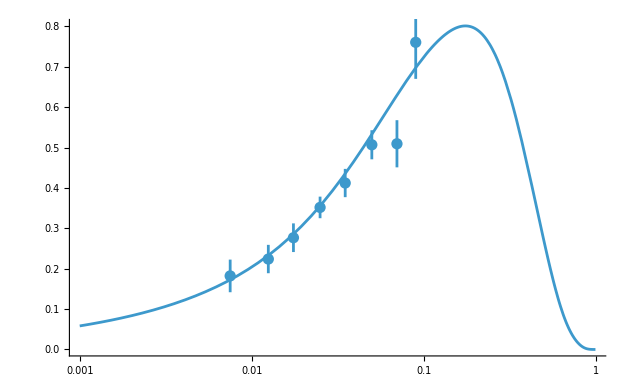

```mathematica
Needs["ErrorBarLogPlots`"]
xf3Q20={{0.0075,0.1821,0.04039},{0.0125,0.2239,0.03512},{0.0175,0.2767,0.03549},{0.025,0.3517,0.0267},{0.035,0.4121,0.035},{0.05,0.5068,0.036},{0.07,0.5093,0.05839},{0.09,0.7605,0.09046}};
ErrorListLogLinearPlot[xf3Q20];
LogLinearPlot[xF3xQ/.f->4/.Q->20,{x,0.001,0.999}];
Show[%,%%]
```

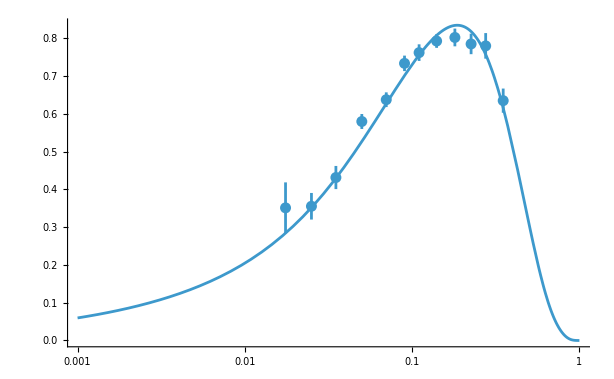

```mathematica
Needs["ErrorBarLogPlots`"]
xf3Q7p9={{0.0175,0.3513,0.06743},{0.025,0.3555,0.03521},{0.035,0.4316,0.03064},{0.05,0.58,0.01979},{0.07,0.6377,0.01946},{0.09,0.734,0.02048},{0.11,0.7624,0.022},{0.14,0.7931,0.01804},{0.18,0.8026,0.02349},{0.225,0.7854,0.0271},{0.275,0.7803,0.03387},{0.35,0.6352,0.03202}};
ErrorListLogLinearPlot[xf3Q7p9];
LogLinearPlot[xF3xQ/.f->4/.Q->7.9,{x,0.001,0.999}];
Show[%,%%]
```

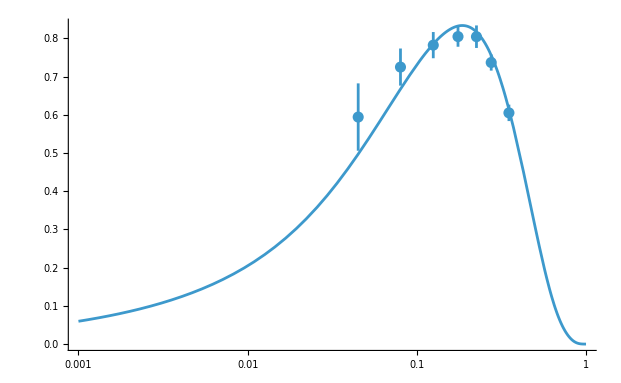

```mathematica
xf3Q8p155={{0.045,0.5941,0.08812945},{0.08,0.7249,0.048568405},{0.125,0.7823,0.03428644},{0.175,0.8047,0.026575365},{0.225,0.8044,0.029471681},{0.275,0.7368,0.02116034},{0.35,0.6051,0.0215}};
ErrorListLogLinearPlot[xf3Q8p155];
LogLinearPlot[xF3xQ/.f->4/.Q->8.155,{x,0.001,0.999}];
Show[%,%%]
```

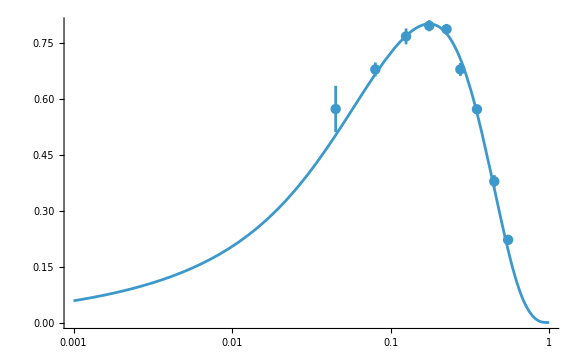

```mathematica
xf3Q19p952={{0.045,0.5729,0.062181669},{0.08,0.679,0.018713899},{0.125,0.7677,0.021220038},{0.175,0.7962,0.014817557},{0.225,0.7871,0.014024265},{0.275,0.6791,0.017284965},{0.35,0.5721,0.011203571},{0.45,0.3787,0.016790771},{0.55,0.2219,0.012518786}};
ErrorListLogLinearPlot[xf3Q19p952];
LogLinearPlot[xF3xQ/.f->4/.Q->19.952,{x,0.001,0.999}];
Show[%,%%]
```

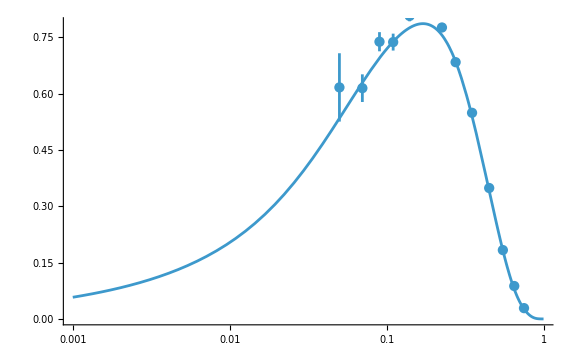

```mathematica
xf3Q31p6={{0.05,0.6167,0.09101},{0.07,0.6147,0.03683},{0.09,0.7384,0.02551},{0.11,0.7374,0.02253},{0.14,0.8071,0.01419},{0.18,0.828,0.01303},{0.225,0.7763,0.01066},{0.275,0.6839,0.01017},{0.35,0.549,0.006821},{0.45,0.3487,0.006094},{0.55,0.1834,0.005175},{0.65,0.08762,0.003702},{0.75,0.02875,0.002163}};
ErrorListLogLinearPlot[xf3Q31p6];
LogLinearPlot[xF3xQ/.f->4/.Q->31.6,{x,0.001,0.999}];
Show[%,%%]
```

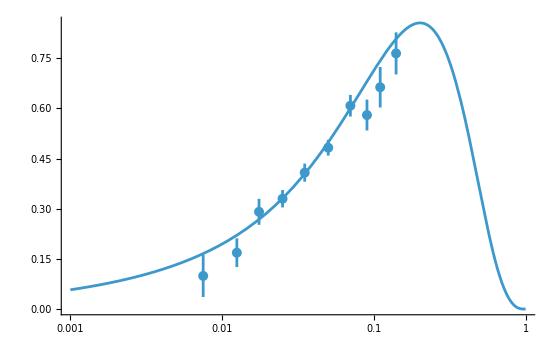

```mathematica
xf3Q3p2={{0.0075,0.09905,0.06319},{0.0125,0.1684,0.0429},{0.0175,0.2906,0.03887},{0.025,0.3298,0.02605},{0.035,0.4078,0.02699},{0.05,0.4822,0.02357},{0.07,0.6078,0.03228},{0.09,0.5799,0.04613},{0.11,0.663,0.06051},{0.14,0.7642,0.06294}};
ErrorListLogLinearPlot[xf3Q3p2];
LogLinearPlot[xF3xQ/.f->3/.Q->3.2,{x,0.001,0.999}];
Show[%,%%]
```

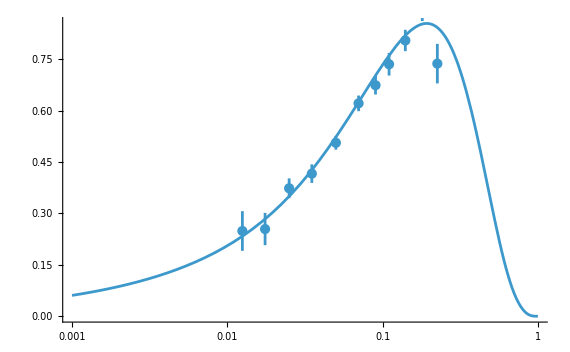

```mathematica
xf3Q5={{0.0125,0.2486,0.05783},{0.0175,0.2543,0.04715},{0.025,0.3732,0.02882},{0.035,0.4159,0.02706},{0.05,0.5058,0.01989},{0.07,0.6209,0.0228},{0.09,0.6738,0.02707},{0.11,0.735,0.03292},{0.14,0.8043,0.0312},{0.18,0.9044,0.04342},{0.225,0.7368,0.05772}};
ErrorListLogLinearPlot[xf3Q5];
LogLinearPlot[xF3xQ/.f->4/.Q->5,{x,0.001,0.999}];
Show[%,%%]
```

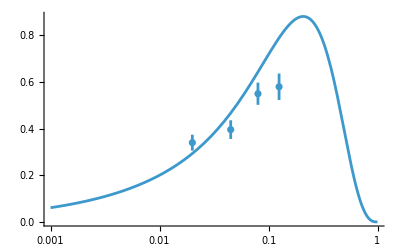

```mathematica
xf3datachorusQ2p052={{0.02,0.3398,0.033922854},{0.045,0.3957,0.04},{0.08,0.5495,0.047590335},{0.125,0.5793,0.056741607}};
ErrorListLogLinearPlot[%];
LogLinearPlot[xF3xQ/.f->3/.Q->2.052,{x,0.001,0.999}];
Show[%,%%]
```

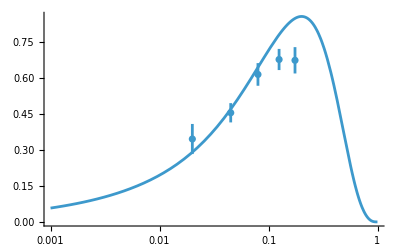

```mathematica
xf3datachorusQ3p25={{0.02,0.3448,0.062542466},{0.045,0.4539,0.040078049},{0.08,0.6133,0.047093524},{0.125,0.6755,0.043990567},{0.175,0.6721,0.054753265}};
ErrorListLogLinearPlot[%];
LogLinearPlot[xF3xQ/.f->3/.Q->3.25,{x,0.001,0.999}];
Show[%,%%]
```

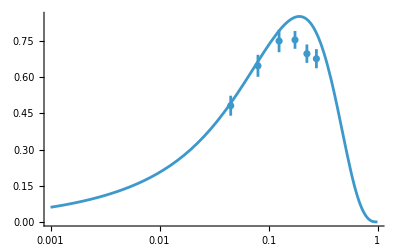

```mathematica
xf3datachorusQ5p146={{0.045,0.4823,0.04148795},{0.08,0.6478,0.045617979},{0.125,0.7509,0.046617164},{0.175,0.7554,0.036962819},{0.225,0.6982,0.038220544},{0.275,0.6773,0.0397}};
ErrorListLogLinearPlot[%];
LogLinearPlot[xF3xQ/.f->4/.Q->5.146,{x,0.001,0.999}];
Show[%,%%]
```

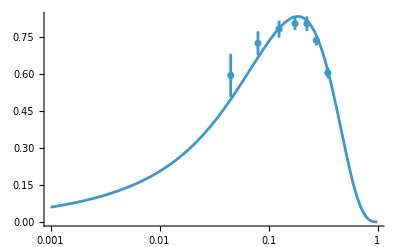

```mathematica
xf3datachorusQ8p155={{0.045,0.5941,0.08812945},{0.08,0.7249,0.048568405},{0.125,0.7823,0.03428644},{0.175,0.8047,0.026575365},{0.225,0.8044,0.029471681},{0.275,0.7368,0.02116034},{0.35,0.6051,0.0215}};
ErrorListLogLinearPlot[%];
LogLinearPlot[xF3xQ/.f->4/.Q->8.155,{x,0.001,0.999}];
Show[%,%%]
```

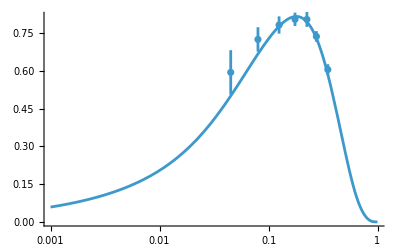

```mathematica
xf3datachorusQ12p925={{0.045,0.5941,0.08812945},{0.08,0.7249,0.048568405},{0.125,0.7823,0.03428644},{0.175,0.8047,0.026575365},{0.225,0.8044,0.029471681},{0.275,0.7368,0.02116034},{0.35,0.6051,0.0215}};
ErrorListLogLinearPlot[%];
LogLinearPlot[xF3xQ/.f->4/.Q->12.925,{x,0.001,0.999}];
Show[%,%%]
```

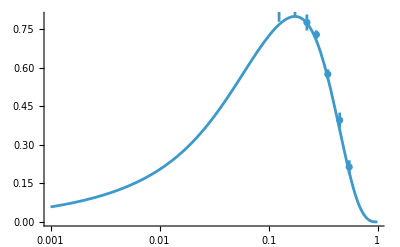

```mathematica
xf3datachorusQ20p52={{0.125,0.8431,0.063238754},{0.175,0.8352,0.03508903},{0.225,0.7768,0.031170018},{0.275,0.7297,0.016164467},{0.35,0.5753,0.019007893},{0.45,0.3962,0.02964473},{0.55,0.2138,0.026340273}};
ErrorListLogLinearPlot[%];
LogLinearPlot[xF3xQ/.f->4/.Q->20.52,{x,0.001,0.999}];
Show[%,%%]
```

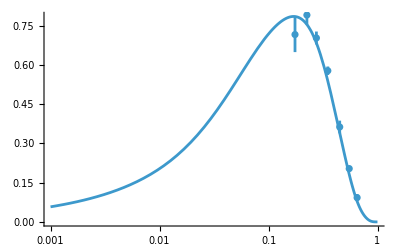

```mathematica
xf3datachorusQ32p5={{0.175,0.7165,0.067128012},{0.225,0.7911,0.036565831},{0.275,0.7034,0.024644675},{0.35,0.5781,0.016124515},{0.45,0.363,0.024223129},{0.55,0.2038,0.01077033},{0.65,0.0928,0.013703284}};
ErrorListLogLinearPlot[%];
LogLinearPlot[xF3xQ/.f->4/.Q->32.5,{x,0.001,0.999}];
Show[%,%%]
```

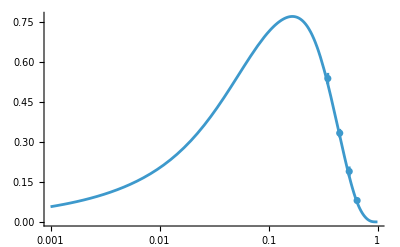

```mathematica
xf3datachorusQ51p455={{0.35,0.5391,0.021023796},{0.45,0.3338,0.015809491},{0.55,0.1898,0.0185},{0.65,0.0803,0.010469479}};
ErrorListLogLinearPlot[%];
LogLinearPlot[xF3xQ/.f->4/.Q->51.455,{x,0.001,0.999}];
Show[%,%%]
```

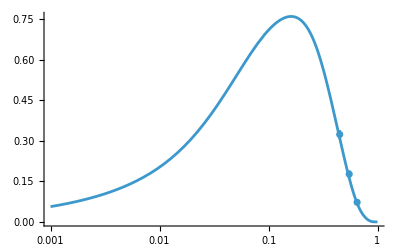

```mathematica
xf3datachorusQ81p55={{0.45,0.3234,0.015929846},{0.55,0.1767,0.013780058},{0.65,0.0725,0.0086539}};
ErrorListLogLinearPlot[%];
LogLinearPlot[xF3xQ/.f->4/.Q->81.55,{x,0.001,0.999}];
Show[%,%%]
```

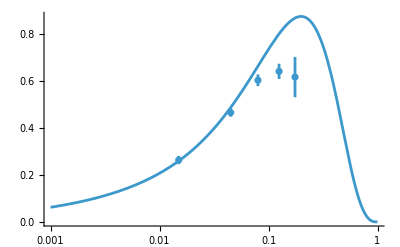

```mathematica
xf3dataNuTeVQ3p162={{0.015,0.2634,0.017717788},{0.045,0.4655,0.017713554},{0.08,0.6031,0.024899799},{0.125,0.641,0.032422986},{0.175,0.6167,0.085731091}};
ErrorListLogLinearPlot[%];
LogLinearPlot[xF3xQ/.f->4/.Q->3.162,{x,0.001,0.999}];
Show[%,%%]
```

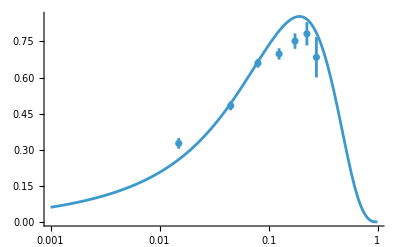

```mathematica
xf3dataNuTeVQ5p012={{0.015,0.3262,0.022040871},{0.045,0.4829,0.018944392},{0.08,0.6596,0.018292621},{0.125,0.698,0.023652695},{0.175,0.7514,0.032137828},{0.225,0.7818,0.048489277},{0.275,0.6842,0.083944982}};
ErrorListLogLinearPlot[%];
LogLinearPlot[xF3xQ/.f->4/.Q->5.012,{x,0.001,0.999}];
Show[%,%%]
```

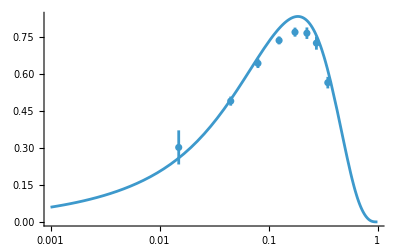

```mathematica
xf3dataNuTeVQ7p943={{0.015,0.3026,0.0692943},{0.045,0.4908,0.018509727},{0.08,0.6441,0.018894973},{0.125,0.7373,0.016118002},{0.175,0.771,0.018348024},{0.225,0.7667,0.02330751},{0.275,0.7264,0.026644699},{0.35,0.5658,0.023479566}};
ErrorListLogLinearPlot[%];
LogLinearPlot[xF3xQ/.f->4/.Q->7.943,{x,0.001,0.999}];
Show[%,%%]
```

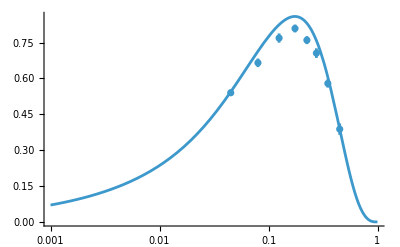

```mathematica
xf3dataNuTeVQ12p589={{0.045,0.54,0.012608331},{0.08,0.6651,0.017859451},{0.125,0.7687,0.019229405},{0.175,0.8087,0.016442932},{0.225,0.76,0.01653844},{0.275,0.7057,0.020111191},{0.35,0.5789,0.017388789},{0.45,0.3878,0.02367467}};
ErrorListLogLinearPlot[%];
LogLinearPlot[xF3xQ/.f->5/.Q->12.589,{x,0.001,0.999}];
Show[%,%%]
```

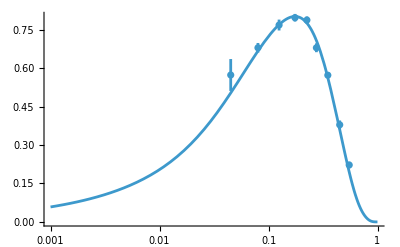

```mathematica
xf3dataNuTeVQ19p952={{0.045,0.5729,0.062181669},{0.08,0.679,0.018713899},{0.125,0.7677,0.021220038},{0.175,0.7962,0.014817557},{0.225,0.7871,0.014024265},{0.275,0.6791,0.017284965},{0.35,0.5721,0.011203571},{0.45,0.3787,0.016790771},{0.55,0.2219,0.012518786}};
ErrorListLogLinearPlot[%];
LogLinearPlot[xF3xQ/.f->4/.Q->19.952,{x,0.001,0.999}];
Show[%,%%]
```

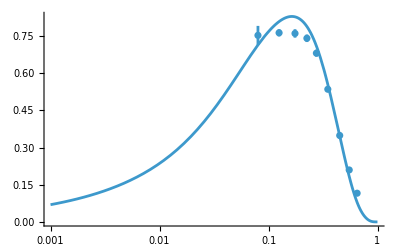

```mathematica
xf3dataNuTeVQ31p622={{0.08,0.7531,0.038191884},{0.125,0.7634,0.0145},{0.175,0.7608,0.017046407},{0.225,0.7413,0.015138692},{0.275,0.6812,0.01385785},{0.35,0.5355,0.009053729},{0.45,0.3489,0.012938315},{0.55,0.2097,0.008013738},{0.65,0.1158,0.007993748}};
ErrorListLogLinearPlot[%];
LogLinearPlot[xF3xQ/.f->5/.Q->31.622,{x,0.001,0.999}];
Show[%,%%]
```

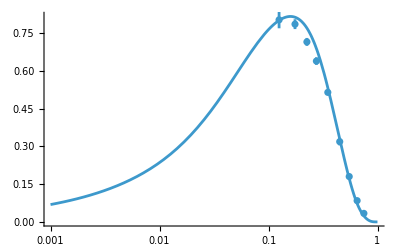

```mathematica
xf3dataNuTeVQ50p118={{0.125,0.8024,0.03345355},{0.175,0.7853,0.019519221},{0.225,0.7149,0.015636496},{0.275,0.6387,0.014903355},{0.35,0.5144,0.010024969},{0.45,0.3187,0.014701701},{0.55,0.1801,0.010396153},{0.65,0.0844,0.006878227},{0.75,0.0338,0.004890808}};
ErrorListLogLinearPlot[%];
LogLinearPlot[xF3xQ/.f->5/.Q->50.118,{x,0.001,0.999}];
Show[%,%%]
```

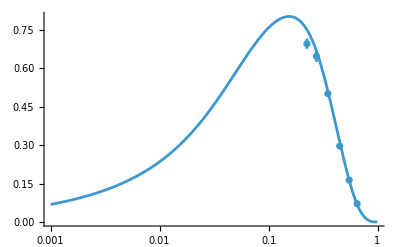

```mathematica
xf3dataNuTeVQ79p432={{0.225,0.6968,0.020329535},{0.275,0.648,0.022387497},{0.35,0.5018,0.008210968},{0.45,0.2965,0.008000625},{0.55,0.1635,0.006745369},{0.65,0.0713,0.006289674}};
ErrorListLogLinearPlot[%];
LogLinearPlot[xF3xQ/.f->5/.Q->79.432,{x,0.001,0.999}];
Show[%,%%]
```

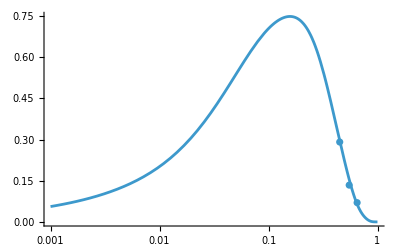

```mathematica
xf3dataNuTeVQ125p89={{0.45,0.2913,0.010435037},{0.55,0.1341,0.01007075},{0.65,0.0702,0.008610459}};
ErrorListLogLinearPlot[%];
LogLinearPlot[xF3xQ/.f->4/.Q->125.89,{x,0.001,0.999}];
Show[%,%%]
```